id/dx j=Piecewise[{{(k^+)_(i,n), j=i+n}, {(k^-)_(i,n), j=i-n}, {0, else}}]

```mathematica
NotebookRead@PreviousCell[]//mathJAXExport[#, "$$\n``\n$$"]&
```

$$\n\langle i|x^n|j\rangle =\n\begin{cases}\n k^+_{i,n} & j=i+n \\\n k^-_{i,n} & j=i-n \\\n 0 & \text{else}\n\end{cases}\n$$

```mathematica
PDF[NormalDistribution[], x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
With[{bleh=PDF[NormalDistribution[], x]},
D[HermiteH[n, x]*bleh, {x, 1}]/.ⅇ^(-x^2/2)->√(2 π)NormalDistribution[]
]//Simplify
```

(2 n HermiteH[-1+n,x]-x HermiteH[n,x]) NormalDistribution[0,1]

```mathematica
{HermiteH[1,x], x*HermiteH[2, x],  HermiteH[3,x]}
```

{2 x,x (-2+4 x^2),-12 x+8 x^3}

```mathematica
{x*HermiteH[2, x],  HermiteH[3,x]}
```

```mathematica
x HermiteH[n,x]
```

x HermiteH[n,x]

```mathematica
With[{bleh=PDF[NormalDistribution[], x]},
D[HermiteH[n, x]*bleh, {x, 2}]/.ⅇ^(-x^2/2)->√(2 π)NormalDistribution[]
]//Simplify
```

(4 (-1+n) n HermiteH[-2+n,x]-4 n x HermiteH[-1+n,x]+(-1+x^2) HermiteH[n,x]) NormalDistribution[0,1]

```mathematica
#.#&@SparseArray[
{
Band[{1, 2}]->Thread[k["+"][Range[5]]],
Band[{2, 1}]->Thread[k["-"][Range[5]]]
}
]//MatrixForm
```

(k[-][1] k[+][1] | 0 | k[+][1] k[+][2] | 0 | 0 | 0
0 | k[-][1] k[+][1]+k[-][2] k[+][2] | 0 | k[+][2] k[+][3] | 0 | 0
k[-][1] k[-][2] | 0 | k[-][2] k[+][2]+k[-][3] k[+][3] | 0 | k[+][3] k[+][4] | 0
0 | k[-][2] k[-][3] | 0 | k[-][3] k[+][3]+k[-][4] k[+][4] | 0 | k[+][4] k[+][5]
0 | 0 | k[-][3] k[-][4] | 0 | k[-][4] k[+][4]+k[-][5] k[+][5] | 0
0 | 0 | 0 | k[-][4] k[-][5] | 0 | k[-][5] k[+][5])

V(x)=∑_(n=0) v_n x^n

```mathematica
NotebookRead@PreviousCell[]//mathJAXExport[#, "$$\n``\n$$"]&
```

$$
V(x)=\sum _{n=0} \, \, v_nx^n
$$

∫_0^(2π) ϕ_n cos(kτ)ϕ_m=∫_0^(2π) ϕ_n ϕ_m(ϕ_k-ϕ_-k)=∫_0^(2π) ϕ_(n+m+k)-ϕ_(n+m-k)

```mathematica
pib[n_, L_:L]=√(2/L)Sin[(n π)/L#]&;
```

```mathematica
Integrate[pib[1][x]*x*pib[1][x], {x, 0, L}]
```

L/2

```mathematica
Integrate[pib[2][x]*x*pib[2][x], {x, 0, L}]
```

L/2

```mathematica
Integrate[pib[3][x]*x*pib[3][x], {x, 0, L}]
```

L/2

```mathematica
pibEl[n_, m_]:=
Which[
n==m,
L/2,
n>m,
pibEl[m, n],
True,
With[{k=m-n},
If[EvenQ[k], 
0,
pibEl[n, m]=Integrate[pib[n][x]*x*pib[m][x], {x, 0, L}]
]
]
];
PIBTable=Array[pibEl,{25, 25}];
```

```mathematica
Assuming[
n∈Integers&&m∈Integers,
Integrate[pib[n][x]*D[pib[n][x], {x, 2}], {x, 0, L}]
]
```

-(n^2 π^2)/L^2

```mathematica
Assuming[
n∈Integers&&m∈Integers,
Integrate[pib[n][x]*x*pib[m][x], {x, 0, L}]
]
```

(4 (-1+(-1)^(m+n)) L m n)/((m^2-n^2)^2 π^2)

```mathematica
mathJAXExport@NotebookRead[PreviousCell[]]
```

$\frac{4 \left(-1+(-1)^{m+n}\right) L m n}{\left(m^2-n^2\right)^2 \pi ^2}$

```mathematica
sequenceEl[n_, m_]:=
Which[
n==m,
L/2,
n>m,
sequenceEl[m, n],
True,
With[{k=m-n},
If[EvenQ[k], 
0,
-(8 (k n+n^2))/(k^2(k+2 n)^2)L/π^2
]
]
]
```

```mathematica
Table[
Which[
n==m,
1,
n>m,
If[sequenceEl[m, n]=!=0, pibEl[m, n]/sequenceEl[m, n], 1],
True,
If[sequenceEl[m, n]=!=0, pibEl[n, m]/sequenceEl[n, m], 1]
],
{n, 25}, {m, 25}
]//MatrixForm
```

```mathematica
FindSequenceFunction@With[{n=1},
-Extract[PIBTable, Thread[{#, n+#}&@Range[Length[PIBTable]-n]]]/(L/(π^2))
]
```

(8 (#1+#1^2))/(1+2 #1)^2&

```mathematica
FindSequenceFunction@With[{n=3},
-Extract[PIBTable, Thread[{#, n+#}&@Range[Length[PIBTable]-n]]]/(L/(π^2))
]
```

(8 (3 #1+#1^2))/(9 (3+2 #1)^2)&

```mathematica
FindSequenceFunction@With[{n=5},
-Extract[PIBTable, Thread[{#, n+#}&@Range[Length[PIBTable]-n]]]/(L/(π^2))
]
```

(8 (5 #1+#1^2))/(25 (5+2 #1)^2)&

```mathematica
Block[{L=5, maxN=1000},
pibBasis=Table[pib[n][x], {n, maxN}];
pibXRep=
N@Array[
sequenceEl,
{maxN, maxN}
];
{pibDVRPts, pibDVRTransf}=Eigensystem[pibXRep];
pibDVRTransf=pibDVRTransf[[Ordering[pibDVRPts]]];
pibDVRPts=Sort@pibDVRPts;
pibDVRFuncs=Map[Dot[#, pibBasis]&, pibDVRTransf];
pibKE=Transpose[pibDVRTransf].DiagonalMatrix[-Range[maxN]^2*π^2/L^2].pibDVRTransf
];
```

```mathematica
pibKE//MatrixPlot
```

```mathematica
cmDVR=ChemDVRObject["Cartesian1DDVR"];
```

```mathematica
cmKE=cmDVR["KineticEnergy", "Range"->{0 ,5}, "Points"->1000];
```

```mathematica
cmKE[[1, 1]]
```

65665.8

```mathematica
pibRescaledKE=pibKE*(cmKE[[500, 500]]/pibKE[[500, 500]]);
```

```mathematica
wat=(pibRescaledKE[[400;;500, 400;;500]]-cmKE[[400;;500, 400;;500]]);
```

```mathematica
cmKE[[500, 500]]
```

65665.8

```mathematica
-pibKE[[500, 500]]-cmKE[[500, 500]]
```

66176.3

```mathematica
Differences[pibDVRPts]//Round[#, .0001]&
```

```mathematica
With[{N=Length[pibDVRPts], phase=-{1, 1, -1, 1, 1}},
figPlot[
phase*pibDVRFuncs[[{1, 1+Floor[.1*N],  N/2, N-Ceiling[.1*N], N}]]//Evaluate,
{x, 0, 5},
{"x", "ϕ"},
PlotRange->All,
Epilog->{AbsolutePointSize[8], Red, Point[Thread[{pibDVRPts, 0.}]]},
AspectRatio->.8
]
]//imageify//Export[
FileNameJoin@{ParentDirectory@NotebookDirectory[], "img", "dvr_basis.png"}, 
#]&
```

/Users/Mark/Documents/UW/Research/Development/TestsAndRefs/References/img/dvr_basis.png

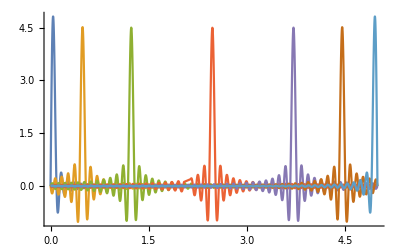

```mathematica
Plot[
{1, 1, 1, 1, -1, 1, -1}*pibDVRFuncs[[{1, 10, 25, 50, 75, 90, 100}]]//Evaluate,
{x, 0, 5},
PlotRange->All
]
```

```mathematica
LegendreP[n,Cos[θ]]*D[LegendreP[n,Cos[θ]], {θ, 2}]
```

```mathematica
Integrate[
LegendreP[n,Cos[θ]]*Cos[θ]*LegendreP[n+1,Cos[θ]]*Sin[θ],
{θ, 0, π}
]
```

$Aborted

```mathematica
Table[
Integrate[
LegendreP[n,Cos[θ]]*LegendreP[n+1,Cos[θ]]*Sin[θ],
{θ, 0, π}
],
{n, 15}
]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[
Integrate[
LegendreP[n,Cos[θ]]*Cos[θ]*LegendreP[n-1,Cos[θ]]*Sin[θ],
{θ, 0, π}
],
{n, 15}
]
```

```mathematica
{2/3,4/15,6/35,8/63,10/99,12/143,14/195,16/255,18/323,20/399,22/483,24/575,26/675,28/783,30/899}//FindSequenceFunction
```

(2 #1)/(-1+4 #1^2)&

```mathematica
l
```

```mathematica
{4/15,6/35,8/63,10/99,12/143,14/195,16/255,18/323,20/399,22/483,24/575,26/675,28/783,30/899,32/1023}//FindSequenceFunction
```

(2 (1+#1))/(3+8 #1+4 #1^2)&

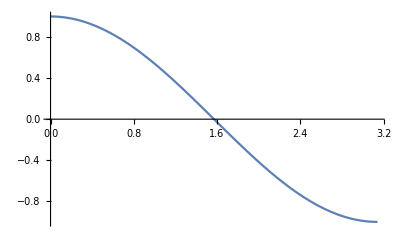

```mathematica
Plot[LegendreP[1, Cos[θ]], {θ, 0, π}]
```

```mathematica
legBasis=Map[LegendreQ[#, Cos[θ]]&, Range[80]];
```

```mathematica
legCoordMat=With[{x=Sqrt[#^2/((2#+1)(2#-1))]&[Range[50]]},
N@SparseArray[
{
Band[{2, 1}]->x,
Band[{1, 2}]->x
}
]
];
{legDVRPts, legDVRMat}=legCoordMat//Normal//Eigensystem;
legDVRPts=ArcCos[legDVRPts];
legDVRMat=legDVRMat[[Ordering[legDVRPts]]];
legDVRPts=Sort@legDVRPts;
```

```mathematica
legFunc=Map[Dot[#, legBasis[[;;Length[legDVRMat]]]]&, legDVRMat];
```

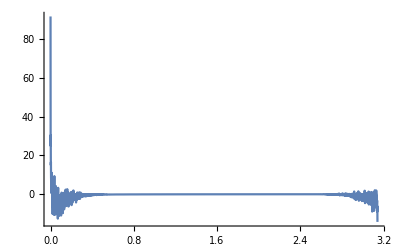

```mathematica
Plot[
legFunc[[1]]//Evaluate, 
{θ, 0, π},
PlotRange->All
]
```

```mathematica
Table[
Integrate[
LegendreP[n,Cos[θ]]*Cos[θ]*LegendreP[n+1,Cos[θ]]*Sin[θ],
{θ, -π, π}
],
{n, 1, 10}
]
```

{0,0,0,0,0,0,0,0,0,0}

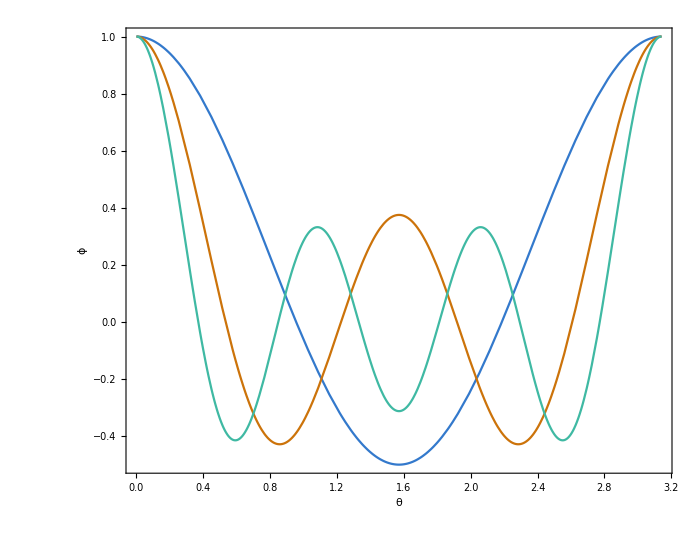

```mathematica
figPlot[
Table[LegendreP[n,Cos[θ]], {n, 2, 6, 2}]//Evaluate,
{θ, 0, π},
{"θ", "ϕ"},
PlotRange->All,(*
Epilog->{AbsolutePointSize[8], Red, Point[Thread[{pibDVRPts, 0.}]]},*)
AspectRatio->.8
]
```

```mathematica
//imageify//Export[
FileNameJoin@{ParentDirectory@NotebookDirectory[], "img", "dvr_basis.png"}, 
#]&
```

```mathematica
chebBasis=Table[ChebyshevT[n, Cos[θ]], {n, 0, 100}];
```

```mathematica
With[{maxN=5},
chebCoordMat=N@SparseArray[
{
Band[{1, 2}]->Map[ (-If[#==1, 1/√2, 1/2]&), Range[maxN]],
Band[{2, 1}]->Map[ (-If[#==1, 1/√2, 1/2]&), Range[maxN]]
}
];
{chebDVRPts, chebDVRMat}=chebCoordMat//Normal//Eigensystem;
chebDVRPts=ArcCos[chebDVRPts];
chebDVRMat=chebDVRMat[[Ordering[chebDVRPts]]];
chebDVRPts=Sort@chebDVRPts;
];
chebFunc=Dot[chebDVRMat, chebBasis[[;;Length[chebDVRMat]]]];
```